```mathematica
<< "/Users/oliviercroissant/Documents/Math/NumericalIntegration.m"
```

```mathematica
<< "/Users/oliviercroissant/Documents/Math/My Documents\\BS.m"
```

```mathematica
<< "/Users/oliviercroissant/Documents/Math/Heston_Definitif5.m"
```

```mathematica
Needs["PlotLegends`"]
```

## Vanilla Spreadoption: payoff=(S_1-S_2-K)^+

S=0.05
0.03 Σ=(0.04 | 0.0268328
0.0268328 | 0.05)M=(-0.01 | 0.00424264
-0.00424264 | -0.02) Σinf=(0.03 | 0.0280571
0.0280571 | 0.041) Q=(0.00269046 | 0.0059101
0. | 0.00162239) ρ=0.5
0.8 Imaginary Shifts=1.1
1.2

{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}={18,12,4.45823,4.45823,0.00001,10}{NbLegCoef2,period2,period2n,ϵ2}={18,6.68734,0.668734,0.00001}

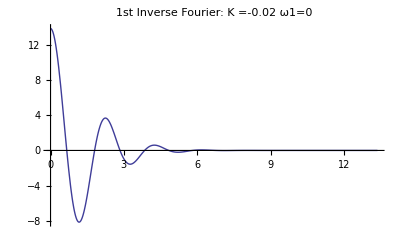
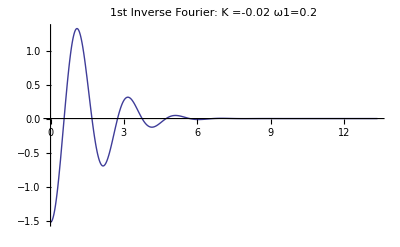
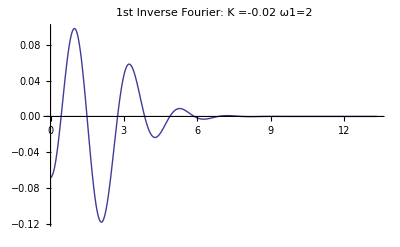

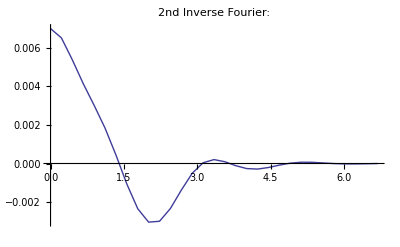

{23.681,0.0401203}

```mathematica
Timing[Module[{S1=0.05,S2=0.03,K=-0.02,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,ν1=0.01,ν2=0.01,M,Σinf,Σ,Q,βm,S,ρ,printflag={1,2,4,6}},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
BiHestonVanilla[S,K,τ,Σ,M,Σinf,β,ρ,printflag]]]
```

S=0.05
0.05 Σ=(0.04 | 0.0268328
0.0268328 | 0.05)M=(-0.01 | 0.00424264
-0.00424264 | -0.02) Σinf=(0.03 | 0.0280571
0.0280571 | 0.041) Q=(0.002 | 0.004
0. | 0.001) ρ=0.5
0.8 Imaginary Shifts=1.1
1.2

{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}={12,8,4.45823,4.45823,0.00001,10}{NbLegCoef2,period2,period2n,ϵ2}={10,6.68734,0.668734,0.00001}

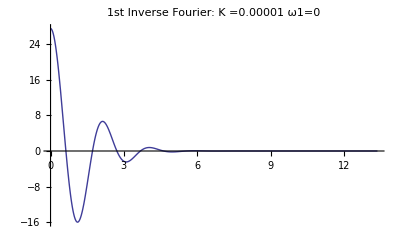
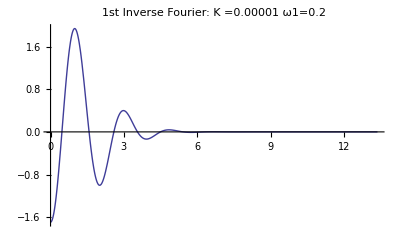
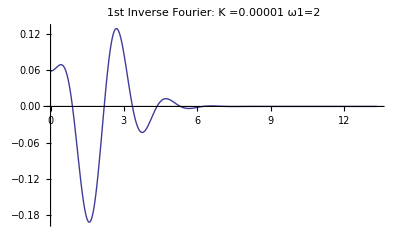

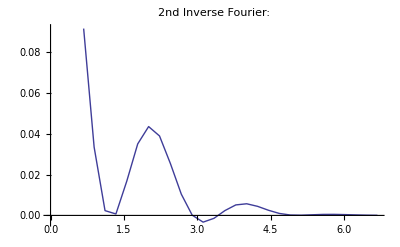

{26.13,0.00954093}

```mathematica
Timing[Module[{S1=0.05,S2=0.05,K=0.00001,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,τ=5,λ1=1.1,λ2=1.2,Q,M,Σinf,Σ,βm,S,ρ,printflag={1,2,4,6}},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
Q=({{0.0026904562514984886, 0.005910101619402922}, {0., 0.0016223883650666592}});Q=({{0.002, 0.004}, {0., 0.001}});

BiHestonVanilla2[S,K,τ,Σ,M,Σinf,Q,ρ,printflag]
]]
```

```mathematica
(*  utilise le beta comme source de vol de vol *)
```

```mathematica
BiHestonVanilla[S_,K_,τ_,Σ_,M_,Σinf_,β_,ρ_,printflag_]:=Module[{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,Q},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,K,τ,Σ,M,Σinf,Q,ρ,"VanillaSpreadoption"];
BiHestonVanilla[S,K,τ,Σ,M,Σinf,Q,ρ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax},{LegendreCoef2,period2,period2n,ϵ2},printflag]
]
```

```mathematica
(* utilise une matrice complete  comme vol de vol *)
```

```mathematica
BiHestonVanilla2[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,printflag_]:=Module[{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,βm},
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,K,τ,Σ,M,Σinf,Q,ρ,"VanillaSpreadoption"];
βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
BiHestonVanilla2[S,K,τ,Σ,M,Σinf,Q,ρ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax},{LegendreCoef2,period2,period2n,ϵ2},printflag]
]
```

```mathematica
BiHestonVanilla[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=BiHestonVanillaAux[S,K,τ,Σ,M,Σinf,Q,ρ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax},{LegendreCoef2,period2,period2n,ϵ2},printflag] /; K≥0
```

```mathematica
BiHestonVanilla[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=BiHestonVanillaAux[S,K,τ,Σ,M,Σinf,Q,ρ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax},{LegendreCoef2,period2,period2n,ϵ2},printflag]+S[[1]]-S[[2]]-K/; K<0
```

```mathematica
BiHestonVanilla2[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=BiHestonVanillaAux2[S,K,τ,Σ,M,Σinf,Q,ρ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax},{LegendreCoef2,period2,period2n,ϵ2},printflag] /; K≥0
```

```mathematica
BiHestonVanilla2[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=BiHestonVanillaAux2[S,K,τ,Σ,M,Σinf,Q,ρ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax},{LegendreCoef2,period2,period2n,ϵ2},printflag]+S[[1]]-S[[2]]-K/; K<0
```

```mathematica
BiHestonVanillaAux[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=
2/(2π)^2 Module[{a,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // ColumnForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//ColumnForm," Imaginary Shifts=",{λ1,λ2} // ColumnForm];
Print["{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}=",{Length[LegendreCoef1],Length[LegendreCoef1n],period1,period1n,ϵ1,imax},"{NbLegCoef2,period2,period2n,ϵ2}=",{Length[LegendreCoef2],period2,period2n,ϵ2}]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SymetrizedBiHestonVanillaIntegrand[Y,K,τ,Σ,M,Q,ρ,β,λ1,λ2,ω1,ω2],{ω2,0 ,2period2},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[K]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,AdaptativeIntegrate[Function[ω1,SymetrizedBiHestonVanillaIntegrand[Y,K,τ,Σ,M,Q,ρ,β,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax][[2]]},{ω2,0,period2,period2/30}],Joined->True,PlotLabel->"2nd Inverse Fourier:",PlotRange->All]]];
res=AdaptativeIntegrate[Function[ω2,a=AdaptativeIntegrate[Function[ω1,SymetrizedBiHestonVanillaIntegrand[Y,K,τ,Σ,M,Q,ρ,β,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax];If[printflag==7|| MemberQ[printflag,7],Print["Integ_2=",a]];a[[2]]],LegendreCoef2,period2,period2n,ϵ2,imax];
If[printflag==7|| MemberQ[printflag,7],Print["Integ_1=",res]];
res[[2]]]
```

```mathematica
BiHestonVanillaAux2[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=
2/(2π)^2 Module[{a,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // ColumnForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//ColumnForm," Imaginary Shifts=",{λ1,λ2} // ColumnForm];
Print["{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}=",{Length[LegendreCoef1],Length[LegendreCoef1n],period1,period1n,ϵ1,imax},"{NbLegCoef2,period2,period2n,ϵ2}=",{Length[LegendreCoef2],period2,period2n,ϵ2}]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SymetrizedBiHestonVanillaIntegrand2[Y,K,τ,Σ,M,Q,ρ,βm,λ1,λ2,ω1,ω2],{ω2,0 ,2period2},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[K]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,AdaptativeIntegrate[Function[ω1,SymetrizedBiHestonVanillaIntegrand2[Y,K,τ,Σ,M,Q,ρ,βm,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax][[2]]},{ω2,0,period2,period2/30}],Joined->True,PlotLabel->"2nd Inverse Fourier:",PlotRange->All]]];
res=AdaptativeIntegrate[Function[ω2,a=AdaptativeIntegrate[Function[ω1,SymetrizedBiHestonVanillaIntegrand2[Y,K,τ,Σ,M,Q,ρ,βm,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax];If[printflag==2,Print["Integ_2=",a]];a[[2]]],LegendreCoef2,period2,period2n,ϵ2,imax];
If[printflag==2,Print["Integ_1=",res]];
res[[2]]]
```

```mathematica
SymetrizedBiHestonVanillaIntegrand[Y_,K_,τ_,Σ_,M_,Q_,ρ_,β_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk2= (-ω2+ⅈ λ2),Sk1A=(-ω1+ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2-ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[If[K>0,
α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},β,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];
α propagatorDroit VanillaPayOffFourierDroite[k1,k2,K]+
Symα SympropagatorDroit VanillaPayOffFourierDroite[Sk1,k2,K]+
αA propagatorGauche VanillaPayOffFourierGauche[k1,k2A,K]+
SymαA SympropagatorGauche VanillaPayOffFourierGauche[Sk1A,k2A,K],
If[K<0,
α2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2);αA2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2A);Symα2=ⅇ^(-ⅈ x2 Sk1-ⅈ x1 k2);SymαA2=ⅇ^(-ⅈ x2 Sk1A-ⅈ x1 k2A);
propagatorDroit2=BiHestonLaplaceQuickTransformReverse[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit2=BiHestonLaplaceQuickTransformReverse[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche2=BiHestonLaplaceQuickTransformReverse[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},β,τ];SympropagatorGauche2=BiHestonLaplaceQuickTransformReverse[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];(α2 (propagatorDroit2 (VanillaPayOffFourierDroite[k1,k2,-K]))+Symα2 (SympropagatorDroit2(VanillaPayOffFourierDroite[Sk1,k2,-K]))) +
(αA2 propagatorGauche2( VanillaPayOffFourierGauche[k1,k2A,-K])+SymαA2 SympropagatorGauche2(VanillaPayOffFourierGauche[Sk1A,k2A,-K]))
,
α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},β,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];
α propagatorDroit VanillaPayOffFourierDroite[k1,k2]+
Symα SympropagatorDroit VanillaPayOffFourierDroite[Sk1,k2]+
αA propagatorGauche VanillaPayOffFourierGauche[k1,k2A]+
SymαA SympropagatorGauche VanillaPayOffFourierGauche[Sk1,k2A]]]]]
```

In SymetrizedBiHestonVanillaIntegrand2,  βm  is a matrix

```mathematica
SymetrizedBiHestonVanillaIntegrand2[Y_,K_,τ_,Σ_,M_,Q_,ρ_,βm_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk2= (-ω2+ⅈ λ2),Sk1A=(-ω1+ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2-ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[If[K>0,
α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},βm,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},βm,τ];
propagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},βm,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},βm,τ];
α propagatorDroit VanillaPayOffFourierDroite[k1,k2,K]+
Symα SympropagatorDroit VanillaPayOffFourierDroite[Sk1,k2,K]+
αA propagatorGauche VanillaPayOffFourierGauche[k1,k2A,K]+
SymαA SympropagatorGauche VanillaPayOffFourierGauche[Sk1A,k2A,K],
If[K<0,
α2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2);αA2=ⅇ^(-ⅈ x2 k1-ⅈ x1 k2A);Symα2=ⅇ^(-ⅈ x2 Sk1-ⅈ x1 k2);SymαA2=ⅇ^(-ⅈ x2 Sk1A-ⅈ x1 k2A);
propagatorDroit2=BiHestonLaplaceQuickTransformReverse2[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},βm,τ];SympropagatorDroit2=BiHestonLaplaceQuickTransformReverse2[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},βm,τ];
propagatorGauche2=BiHestonLaplaceQuickTransformReverse2[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},βm,τ];SympropagatorGauche2=BiHestonLaplaceQuickTransformReverse2[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},βm,τ];(α2 (propagatorDroit2 (VanillaPayOffFourierDroite[k1,k2,-K]))+Symα2 (SympropagatorDroit2(VanillaPayOffFourierDroite[Sk1,k2,-K]))) +
(αA2 propagatorGauche2( VanillaPayOffFourierGauche[k1,k2A,-K])+SymαA2 SympropagatorGauche2(VanillaPayOffFourierGauche[Sk1A,k2A,-K]))
,
α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},βm,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},βm,τ];
propagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},βm,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},βm,τ];
α propagatorDroit VanillaPayOffFourierDroite[k1,k2]+
Symα SympropagatorDroit VanillaPayOffFourierDroite[Sk1,k2]+
αA propagatorGauche VanillaPayOffFourierGauche[k1,k2A]+
SymαA SympropagatorGauche VanillaPayOffFourierGauche[Sk1,k2A]]]]]
```

```mathematica
BiHestonLaplaceQuickTransform[{{M11_,M12_},{M21_,M22_}},{{Q11_,Q12_},{Q21_,Q22_}},{ρ1_,ρ2_},{{Σ11_,Σ12_},{Σ21_,Σ22_}},{γ1_,γ2_},β_,τ_]:=
Module[{EXPH=MatrixExp[τ{{1/2 (-M11-Q11 γ1 ρ1-Q21 γ1 ρ2),1/2 (-M12-Q11 γ2 ρ1-Q21 γ2 ρ2),1/2 (-Q11^2-Q21^2),1/2 (-Q11 Q12-Q21 Q22)},{1/2 (-M21-Q12 γ1 ρ1-Q22 γ1 ρ2),1/2 (-M22-Q12 γ2 ρ1-Q22 γ2 ρ2),1/2 (-Q11 Q12-Q21 Q22),1/2 (-Q12^2-Q22^2)},{1/2 (-1+γ1) γ1,(γ1 γ2)/2,1/2 (M11+Q11 γ1 ρ1+Q21 γ1 ρ2),1/2 (M21+Q12 γ1 ρ1+Q22 γ1 ρ2)},{(γ1 γ2)/2,1/2 (-1+γ2) γ2,1/2 (M12+Q11 γ2 ρ1+Q21 γ2 ρ2),1/2 (M22+Q12 γ2 ρ1+Q22 γ2 ρ2)}}],δ},
δ=-EXPH[[1,2]] EXPH[[2,1]]+EXPH[[1,1]] EXPH[[2,2]];
Exp[1/δ(EXPH[[2,2]] EXPH[[3,1]] Σ11-EXPH[[1,2]] EXPH[[4,1]] Σ11-EXPH[[2,1]] EXPH[[3,1]] Σ12+EXPH[[2,2]] EXPH[[3,2]] Σ12+
EXPH[[1,1]] EXPH[[4,1]] Σ12-EXPH[[1,2]] EXPH[[4,2]] Σ12-EXPH[[2,1]] EXPH[[3,2]] Σ22+EXPH[[1,1]] EXPH[[4,2]] Σ22)-2 β^2(Log[δ]+τ/2( M11+M22+Q11 γ1 ρ1+Q12 γ2 ρ1+Q21 γ1 ρ2+Q22 γ2 ρ2))]
]
```

the β matrix represents here  (M Σinf+Σinf M )(Q^*Q)^-1

```mathematica
BiHestonLaplaceQuickTransform2[{{M11_,M12_},{M21_,M22_}},{{Q11_,Q12_},{Q21_,Q22_}},{ρ1_,ρ2_},{{Σ11_,Σ12_},{Σ21_,Σ22_}},{γ1_,γ2_},{{β11_,β12_},{β21_,β22_}},τ_]:=
Module[{EXPH=MatrixExp[τ{{1/2 (-M11-Q11 γ1 ρ1-Q21 γ1 ρ2),1/2 (-M12-Q11 γ2 ρ1-Q21 γ2 ρ2),1/2 (-Q11^2-Q21^2),1/2 (-Q11 Q12-Q21 Q22)},{1/2 (-M21-Q12 γ1 ρ1-Q22 γ1 ρ2),1/2 (-M22-Q12 γ2 ρ1-Q22 γ2 ρ2),1/2 (-Q11 Q12-Q21 Q22),1/2 (-Q12^2-Q22^2)},{1/2 (-1+γ1) γ1,(γ1 γ2)/2,1/2 (M11+Q11 γ1 ρ1+Q21 γ1 ρ2),1/2 (M21+Q12 γ1 ρ1+Q22 γ1 ρ2)},{(γ1 γ2)/2,1/2 (-1+γ2) γ2,1/2 (M12+Q11 γ2 ρ1+Q21 γ2 ρ2),1/2 (M22+Q12 γ2 ρ1+Q22 γ2 ρ2)}}],δ,LogA11},
δ=-EXPH[[1,2]] EXPH[[2,1]]+EXPH[[1,1]] EXPH[[2,2]];
LogA11=MatrixLog2[{{EXPH[[1,1]],EXPH[[1,2]]},{EXPH[[2,1]],EXPH[[2,2]]}}];
Exp[1/δ(EXPH[[2,2]] EXPH[[3,1]] Σ11-EXPH[[1,2]] EXPH[[4,1]] Σ11-EXPH[[2,1]] EXPH[[3,1]] Σ12+EXPH[[2,2]] EXPH[[3,2]] Σ12+
EXPH[[1,1]] EXPH[[4,1]] Σ12-EXPH[[1,2]] EXPH[[4,2]] Σ12-EXPH[[2,1]] EXPH[[3,2]] Σ22+EXPH[[1,1]] EXPH[[4,2]] Σ22)-2(β11 LogA11[[1,1]]+β12 LogA11[[1,2]]+β21 LogA11[[2,1]]+β22 LogA11[[2,2]]+1/2 (β11 (M11+Q11 γ1 ρ1+Q21 γ1 ρ2)+β21 (M21+Q12 γ1 ρ1+Q22 γ1 ρ2)+β12 (M12+Q11 γ2 ρ1+Q21 γ2 ρ2)+β22 (M22+Q12 γ2 ρ1+Q22 γ2 ρ2)) τ)]
]
```

the same procedure but where' underlying 1 is echanged with  underlying 2

```mathematica
BiHestonLaplaceQuickTransformReverse[{{M22_,M21_},{M12_,M11_}},{{Q22_,Q21_},{Q12_,Q11_}},{ρ2_,ρ1_},{{Σ22_,Σ21_},{Σ12_,Σ11_}},{γ1_,γ2_},β_,τ_]:=
Module[{EXPH=MatrixExp[τ{{1/2 (-M11-Q11 γ1 ρ1-Q21 γ1 ρ2),1/2 (-M12-Q11 γ2 ρ1-Q21 γ2 ρ2),1/2 (-Q11^2-Q21^2),1/2 (-Q11 Q12-Q21 Q22)},{1/2 (-M21-Q12 γ1 ρ1-Q22 γ1 ρ2),1/2 (-M22-Q12 γ2 ρ1-Q22 γ2 ρ2),1/2 (-Q11 Q12-Q21 Q22),1/2 (-Q12^2-Q22^2)},{1/2 (-1+γ1) γ1,(γ1 γ2)/2,1/2 (M11+Q11 γ1 ρ1+Q21 γ1 ρ2),1/2 (M21+Q12 γ1 ρ1+Q22 γ1 ρ2)},{(γ1 γ2)/2,1/2 (-1+γ2) γ2,1/2 (M12+Q11 γ2 ρ1+Q21 γ2 ρ2),1/2 (M22+Q12 γ2 ρ1+Q22 γ2 ρ2)}}],δ},
δ=-EXPH[[1,2]] EXPH[[2,1]]+EXPH[[1,1]] EXPH[[2,2]];
Exp[1/δ(EXPH[[2,2]] EXPH[[3,1]] Σ11-EXPH[[1,2]] EXPH[[4,1]] Σ11-EXPH[[2,1]] EXPH[[3,1]] Σ12+EXPH[[2,2]] EXPH[[3,2]] Σ12+
EXPH[[1,1]] EXPH[[4,1]] Σ12-EXPH[[1,2]] EXPH[[4,2]] Σ12-EXPH[[2,1]] EXPH[[3,2]] Σ22+EXPH[[1,1]] EXPH[[4,2]] Σ22)-2 β^2(Log[δ]+τ/2( M11+M22+Q11 γ1 ρ1+Q12 γ2 ρ1+Q21 γ1 ρ2+Q22 γ2 ρ2))]
]
```

```mathematica
BiHestonLaplaceQuickTransformReverse2[{{M22_,M21_},{M12_,M11_}},{{Q22_,Q21_},{Q12_,Q11_}},{ρ2_,ρ1_},{{Σ22_,Σ21_},{Σ12_,Σ11_}},{γ1_,γ2_},{{β11_,β12_},{β21_,β22_}},τ_]:=
Module[{EXPH=MatrixExp[τ{{1/2 (-M11-Q11 γ1 ρ1-Q21 γ1 ρ2),1/2 (-M12-Q11 γ2 ρ1-Q21 γ2 ρ2),1/2 (-Q11^2-Q21^2),1/2 (-Q11 Q12-Q21 Q22)},{1/2 (-M21-Q12 γ1 ρ1-Q22 γ1 ρ2),1/2 (-M22-Q12 γ2 ρ1-Q22 γ2 ρ2),1/2 (-Q11 Q12-Q21 Q22),1/2 (-Q12^2-Q22^2)},{1/2 (-1+γ1) γ1,(γ1 γ2)/2,1/2 (M11+Q11 γ1 ρ1+Q21 γ1 ρ2),1/2 (M21+Q12 γ1 ρ1+Q22 γ1 ρ2)},{(γ1 γ2)/2,1/2 (-1+γ2) γ2,1/2 (M12+Q11 γ2 ρ1+Q21 γ2 ρ2),1/2 (M22+Q12 γ2 ρ1+Q22 γ2 ρ2)}}],δ,LogA11},
δ=-EXPH[[1,2]] EXPH[[2,1]]+EXPH[[1,1]] EXPH[[2,2]];
LogA11=MatrixLog2[{{EXPH[[1,1]],EXPH[[1,2]]},{EXPH[[2,1]],EXPH[[2,2]]}}];
Exp[1/δ(EXPH[[2,2]] EXPH[[3,1]] Σ11-EXPH[[1,2]] EXPH[[4,1]] Σ11-EXPH[[2,1]] EXPH[[3,1]] Σ12+EXPH[[2,2]] EXPH[[3,2]] Σ12+
EXPH[[1,1]] EXPH[[4,1]] Σ12-EXPH[[1,2]] EXPH[[4,2]] Σ12-EXPH[[2,1]] EXPH[[3,2]] Σ22+EXPH[[1,1]] EXPH[[4,2]] Σ22)-2(β11 LogA11[[1,1]]+β12 LogA11[[1,2]]+β21 LogA11[[2,1]]+β22 LogA11[[2,2]]+1/2 (β11 (M11+Q11 γ1 ρ1+Q21 γ1 ρ2)+β21 (M21+Q12 γ1 ρ1+Q22 γ1 ρ2)+β12 (M12+Q11 γ2 ρ1+Q21 γ2 ρ2)+β22 (M22+Q12 γ2 ρ1+Q22 γ2 ρ2)) τ)]
]
```

```mathematica
VanillaPayOffFourierDroite[k1_,k2_,K_]:=K^(ⅈ k1)/(k1 (-ⅈ+k1) k2 (-ⅈ+k2))( K^(ⅈ k2+1)/Gamma[-ⅈ k1] ( 
(1+ⅈ k2) Gamma[1+ⅈ k2] ( Gamma[-ⅈ (k1+k2)])+ⅈ  k2 Gamma[2+ⅈ k2] (  Gamma[-ⅈ (-ⅈ+k1+k2)]))-
  (ⅈ  k2 Hypergeometric2F1[-ⅈ k1,1+ⅈ k2,2+ⅈ k2,-1/K]+K (1+ⅈ k2) Hypergeometric2F1[-ⅈ k1,ⅈ k2,1+ⅈ k2,-1/K]))
```

```mathematica
VanillaPayOffFourierDroite[k1_,k2_]:=1/(k1 (-ⅈ+k1) (1+ⅈ k1+ⅈ k2))
```

```mathematica
VanillaPayOffFourierGauche[k1_,k2_,K_]:=K^(ⅈ k1)/(k1 (-ⅈ+k1) k2 (-ⅈ+k2))  (ⅈ  k2 Hypergeometric2F1[-ⅈ k1,1+ⅈ k2,2+ⅈ k2,-1/K]+K (1+ⅈ k2) Hypergeometric2F1[-ⅈ k1,ⅈ k2,1+ⅈ k2,-1/K])
```

```mathematica
VanillaPayOffFourierGauche[k1_,k2_]:=-1/(k1 (-ⅈ+k1) (1+ⅈ k1+ⅈ k2))
```

## Vanilla Underlying 1 Option: payoff=(S_1-K)^+

S=0.01
0.05 Σ=(0.04 | 0.0268328
0.0268328 | 0.05)M=(-0.01 | 0.00424264
-0.00424264 | -0.02) Σinf=(0.03 | 0.0280571
0.0280571 | 0.041) Q=(0.00269046 | 0.0059101
0. | 0.00162239) ρ=0.5
0.8 Imaginary Shifts=1.1
1.2

{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}={12,8,6.68734,6.68734,0.00001,10}{NbLegCoef2,period2,period2n,ϵ2}={12,8.91645,0.891645,0.00001}

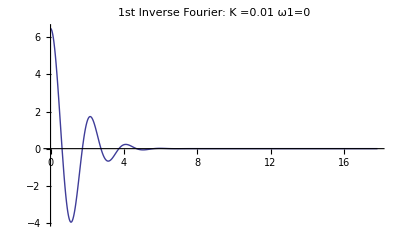
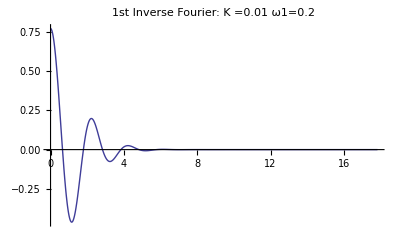
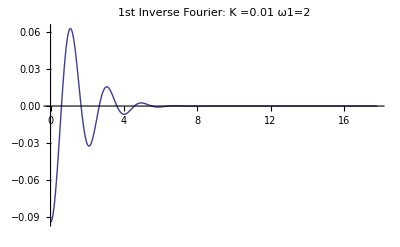

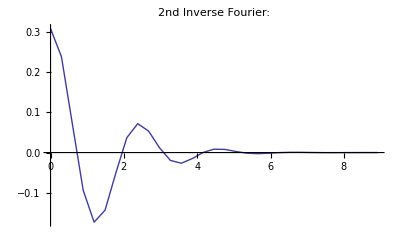

{11.903,0.00198014}

```mathematica
Timing[Module[{S1=0.01,S2=0.05,K=0.01,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,ν1=0.01,ν2=0.01,M,Σinf,Σ,Q,βm,S,ρ,printflag={1,2,4,6}},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
BiHestonUnderlying1Vanilla[S,K,τ,Σ,M,Σinf,β,ρ,printflag]]]
```

S=0.05
0.05 Σ=(0.04 | 0.0268328
0.0268328 | 0.05)M=(-0.01 | 0.00424264
-0.00424264 | -0.02) Σinf=(0.03 | 0.0280571
0.0280571 | 0.041) Q=(0.002 | 0.004
0. | 0.001) ρ=0.5
0.8 Imaginary Shifts=1.1
1.2

{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}={12,8,4.45823,4.45823,0.00001,10}{NbLegCoef2,period2,period2n,ϵ2}={10,6.68734,0.668734,0.00001}

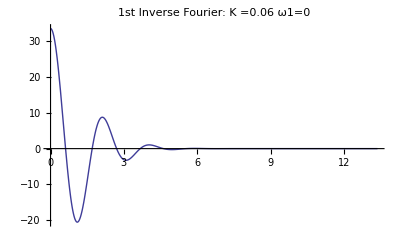
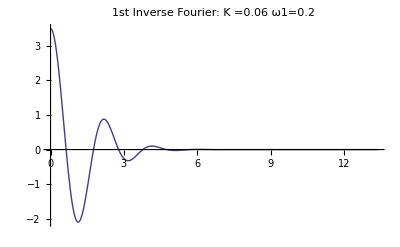
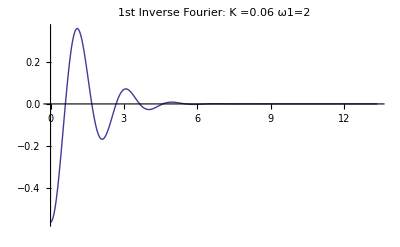

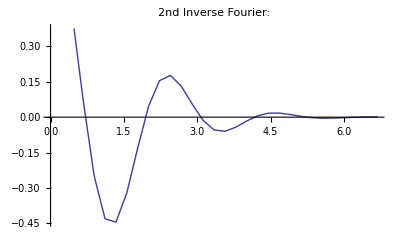

{15.194,0.00537488}

```mathematica
Timing[Module[{S1=0.05,S2=0.05,K=0.06,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,τ=5,λ1=1.1,λ2=1.2,Q,M,Σinf,Σ,βm,S,ρ,printflag={1,2,4,6}},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
Q=({{0.0026904562514984886, 0.005910101619402922}, {0., 0.0016223883650666592}});Q=({{0.002, 0.004}, {0., 0.001}});

BiHestonUnderlying1Vanilla2[S,K,τ,Σ,M,Σinf,Q,ρ,printflag]
]]
```

```mathematica
(*  utilise le beta comme source de vol de vol *)
```

```mathematica
BiHestonUnderlying1Vanilla[S_,K_,τ_,Σ_,M_,Σinf_,β_,ρ_,printflag_]:=Module[{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,Q},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,K,τ,Σ,M,Σinf,Q,ρ,"Underlying1Option"];
BiHestonUnderlying1Vanilla[S,K,τ,Σ,M,Σinf,Q,ρ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax},{LegendreCoef2,period2,period2n,ϵ2},printflag]
]
```

```mathematica
(* utilise une matrice complete  comme vol de vol *)
```

```mathematica
BiHestonUnderlying1Vanilla2[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,printflag_]:=Module[{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,βm},
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,K,τ,Σ,M,Σinf,Q,ρ,"Underlying1Option"];
βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
BiHestonUnderlying1Vanilla2[S,K,τ,Σ,M,Σinf,Q,ρ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax},{LegendreCoef2,period2,period2n,ϵ2},printflag]
]
```

```mathematica
BiHestonUnderlying1Vanilla[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=BiHestonUnderlying1VanillaAux[S,K,τ,Σ,M,Σinf,Q,ρ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax},{LegendreCoef2,period2,period2n,ϵ2},printflag] /; K≥0
```

```mathematica
BiHestonUnderlying1Vanilla2[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=BiHestonUnderlying1VanillaAux2[S,K,τ,Σ,M,Σinf,Q,ρ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax},{LegendreCoef2,period2,period2n,ϵ2},printflag] /; K≥0
```

```mathematica
BiHestonUnderlying1VanillaAux[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=
2/(2π)^2 Module[{a,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // ColumnForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//ColumnForm," Imaginary Shifts=",{λ1,λ2} // ColumnForm];
Print["{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}=",{Length[LegendreCoef1],Length[LegendreCoef1n],period1,period1n,ϵ1,imax},"{NbLegCoef2,period2,period2n,ϵ2}=",{Length[LegendreCoef2],period2,period2n,ϵ2}]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SymetrizedBiHestonUnderlying1VanillaIntegrand[Y,K,τ,Σ,M,Q,ρ,β,λ1,λ2,ω1,ω2],{ω2,0 ,2period2},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[K]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,AdaptativeIntegrate[Function[ω1,SymetrizedBiHestonUnderlying1VanillaIntegrand[Y,K,τ,Σ,M,Q,ρ,β,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax][[2]]},{ω2,0,period2,period2/30}],Joined->True,PlotLabel->"2nd Inverse Fourier:",PlotRange->All]]];
res=AdaptativeIntegrate[Function[ω2,a=AdaptativeIntegrate[Function[ω1,SymetrizedBiHestonUnderlying1VanillaIntegrand[Y,K,τ,Σ,M,Q,ρ,β,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax];If[printflag==7|| MemberQ[printflag,7],Print["Integ_2=",a]];a[[2]]],LegendreCoef2,period2,period2n,ϵ2,imax];
If[printflag==7|| MemberQ[printflag,7],Print["Integ_1=",res]];
res[[2]]]
```

```mathematica
BiHestonUnderlying1VanillaAux2[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=
2/(2π)^2 Module[{a,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // ColumnForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//ColumnForm," Imaginary Shifts=",{λ1,λ2} // ColumnForm];
Print["{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}=",{Length[LegendreCoef1],Length[LegendreCoef1n],period1,period1n,ϵ1,imax},"{NbLegCoef2,period2,period2n,ϵ2}=",{Length[LegendreCoef2],period2,period2n,ϵ2}]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SymetrizedBiHestonUnderlying1VanillaIntegrand2[Y,K,τ,Σ,M,Q,ρ,βm,λ1,λ2,ω1,ω2],{ω2,0 ,2period2},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[K]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,AdaptativeIntegrate[Function[ω1,SymetrizedBiHestonUnderlying1VanillaIntegrand2[Y,K,τ,Σ,M,Q,ρ,βm,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax][[2]]},{ω2,0,period2,period2/30}],Joined->True,PlotLabel->"2nd Inverse Fourier:"]]];
res=AdaptativeIntegrate[Function[ω2,a=AdaptativeIntegrate[Function[ω1,SymetrizedBiHestonUnderlying1VanillaIntegrand2[Y,K,τ,Σ,M,Q,ρ,βm,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax];If[printflag==7|| MemberQ[printflag,7],Print["Integ_2=",a]];a[[2]]],LegendreCoef2,period2,period2n,ϵ2,imax];
If[printflag==7|| MemberQ[printflag,7],Print["Integ_1=",res]];
res[[2]]]
```

```mathematica
SymetrizedBiHestonUnderlying1VanillaIntegrand[Y_,K_,τ_,Σ_,M_,Q_,ρ_,β_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk2= (-ω2+ⅈ λ2),Sk1A=(-ω1+ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2-ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},β,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];
α propagatorDroit FirstUnderlyingVanillaPayOffFourierDroite[k1,k2,K]+
Symα SympropagatorDroit FirstUnderlyingVanillaPayOffFourierDroite[Sk1,k2,K]+
αA propagatorGauche FirstUnderlyingVanillaPayOffFourierGauche[k1,k2A,K]+
SymαA SympropagatorGauche FirstUnderlyingVanillaPayOffFourierGauche[Sk1A,k2A,K]]]
```

```mathematica
SymetrizedBiHestonUnderlying1VanillaIntegrand2[Y_,K_,τ_,Σ_,M_,Q_,ρ_,βm_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk2= (-ω2+ⅈ λ2),Sk1A=(-ω1+ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2-ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},βm,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},βm,τ];
propagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2A},βm,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},βm,τ];
α propagatorDroit FirstUnderlyingVanillaPayOffFourierDroite[k1,k2,K]+
Symα SympropagatorDroit FirstUnderlyingVanillaPayOffFourierDroite[Sk1,k2,K]+
αA propagatorGauche FirstUnderlyingVanillaPayOffFourierGauche[k1,k2A,K]+
SymαA SympropagatorGauche FirstUnderlyingVanillaPayOffFourierGauche[Sk1A,k2A,K]]]
```

```mathematica
FirstUnderlyingVanillaPayOffFourierDroite[k1_,k2_,K_]:=(ⅈ K^(1+ⅈ k1))/(ⅈ k1 k2-k1^2 k2)
```

```mathematica
FirstUnderlyingVanillaPayOffFourierGauche[k1_,k2_,K_]:=-K^(1+ⅈ k1)/(k1 k2+ⅈ k1^2 k2)
```

## Vanilla Underlying 2 Option: payoff=(S_2-K)^+

S=0.05
0.05 Σ=(0.04 | 0.0268328
0.0268328 | 0.05)M=(-0.01 | 0.00424264
-0.00424264 | -0.02) Σinf=(0.03 | 0.0280571
0.0280571 | 0.041) Q=(0.00269046 | 0.0059101
0. | 0.00162239) ρ=0.5
0.8 Imaginary Shifts=1.1
1.2

{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}={12,8,4.45823,4.45823,0.00001,10}{NbLegCoef2,period2,period2n,ϵ2}={10,6.68734,0.668734,0.00001}

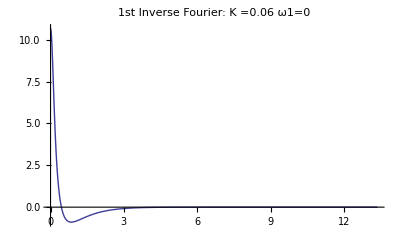
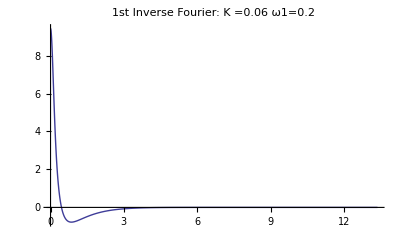
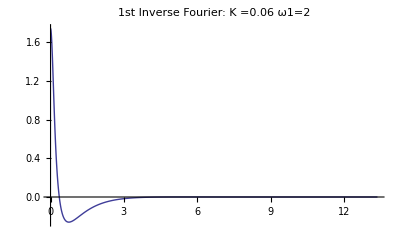

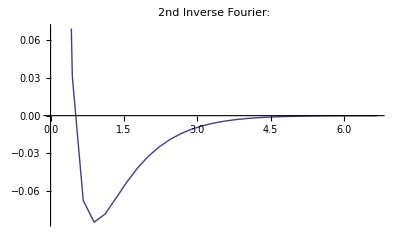

{8.113,0.0071533}

```mathematica
Timing[Module[{S1=0.05,S2=0.05,K=0.06,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,ν1=0.01,ν2=0.01,M,Σinf,Σ,Q,βm,S,ρ,printflag={1,2,4,6}},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
BiHestonUnderlying2Vanilla[S,K,τ,Σ,M,Σinf,β,ρ,printflag]]]
```

S=0.05
0.05 Σ=(0.04 | 0.0268328
0.0268328 | 0.05)M=(-0.01 | 0.00424264
-0.00424264 | -0.02) Σinf=(0.03 | 0.0280571
0.0280571 | 0.041) Q=(0.002 | 0.004
0. | 0.001) ρ=0.5
0.8 Imaginary Shifts=1.1
1.2

{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}={12,8,4.45823,4.45823,0.00001,10}{NbLegCoef2,period2,period2n,ϵ2}={10,6.68734,0.668734,0.00001}

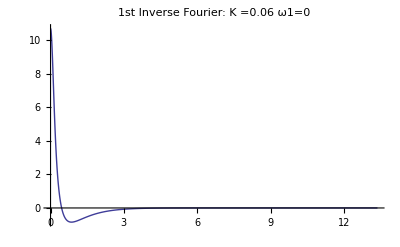
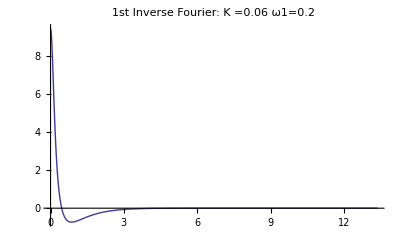
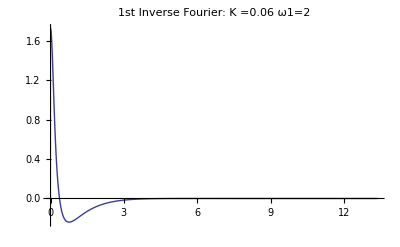

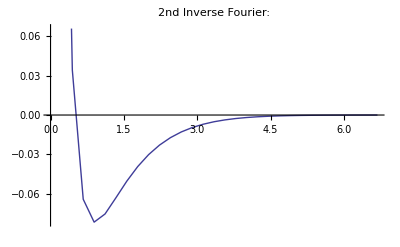

{11.014,0.00755016}

```mathematica
Timing[Module[{S1=0.05,S2=0.05,K=0.06,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,τ=5,λ1=1.1,λ2=1.2,Q,M,Σinf,Σ,βm,S,ρ,printflag={1,2,4,6}},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
Q=({{0.0026904562514984886, 0.005910101619402922}, {0., 0.0016223883650666592}});Q=({{0.002, 0.004}, {0., 0.001}});

BiHestonUnderlying2Vanilla2[S,K,τ,Σ,M,Σinf,Q,ρ,printflag]
]]
```

```mathematica
(*  utilise le beta comme source de vol de vol *)
```

```mathematica
BiHestonUnderlying2Vanilla[S_,K_,τ_,Σ_,M_,Σinf_,β_,ρ_,printflag_]:=Module[{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,Q},
Q=CholeskyDecomposition[-((M.Σinf+Σinf. Transpose[M])/2)]/β;
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,K,τ,Σ,M,Σinf,Q,ρ,"Underlying2Option"];
BiHestonUnderlying2Vanilla[S,K,τ,Σ,M,Σinf,Q,ρ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax},{LegendreCoef2,period2,period2n,ϵ2},printflag]
]
```

```mathematica
(* utilise une matrice complete  comme vol de vol *)
```

```mathematica
BiHestonUnderlying2Vanilla2[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,printflag_]:=Module[{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,LegendreCoef2,period2,period2n,ϵ2,imax,λ1,λ2,βm},
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},imax,λ1,λ2}=BiHestonVanillaOptimalParameters[S,K,τ,Σ,M,Σinf,Q,ρ,"Underlying2Option"];
βm=-((M.Σinf+Σinf.Transpose[M])/2).Inverse[(Transpose[Q].Q)];
BiHestonUnderlying2Vanilla2[S,K,τ,Σ,M,Σinf,Q,ρ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax},{LegendreCoef2,period2,period2n,ϵ2},printflag]
]
```

```mathematica
BiHestonUnderlying2Vanilla[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=BiHestonUnderlying2VanillaAux[S,K,τ,Σ,M,Σinf,Q,ρ,β,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax},{LegendreCoef2,period2,period2n,ϵ2},printflag] /; K≥0
```

```mathematica
BiHestonUnderlying2Vanilla2[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=BiHestonUnderlying2VanillaAux2[S,K,τ,Σ,M,Σinf,Q,ρ,βm,λ1,λ2,{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax},{LegendreCoef2,period2,period2n,ϵ2},printflag] /; K≥0
```

```mathematica
BiHestonUnderlying2VanillaAux[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,β_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=
2/(2π)^2 Module[{a,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // ColumnForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//ColumnForm," Imaginary Shifts=",{λ1,λ2} // ColumnForm];
Print["{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}=",{Length[LegendreCoef1],Length[LegendreCoef1n],period1,period1n,ϵ1,imax},"{NbLegCoef2,period2,period2n,ϵ2}=",{Length[LegendreCoef2],period2,period2n,ϵ2}]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SymetrizedBiHestonUnderlying2VanillaIntegrand[Y,K,τ,Σ,M,Q,ρ,β,λ1,λ2,ω1,ω2],{ω2,0 ,2period2},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[K]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,AdaptativeIntegrate[Function[ω1,SymetrizedBiHestonUnderlying2VanillaIntegrand[Y,K,τ,Σ,M,Q,ρ,β,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax][[2]]},{ω2,0,period2,period2/30}],Joined->True,PlotLabel->"2nd Inverse Fourier:",PlotRange->All]]];
res=AdaptativeIntegrate[Function[ω2,a=AdaptativeIntegrate[Function[ω1,SymetrizedBiHestonUnderlying2VanillaIntegrand[Y,K,τ,Σ,M,Q,ρ,β,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax];If[printflag==7|| MemberQ[printflag,7],Print["Integ_2=",a]];a[[2]]],LegendreCoef2,period2,period2n,ϵ2,imax];
If[printflag==7|| MemberQ[printflag,7],Print["Integ_1=",res]];
res[[2]]]
```

```mathematica
BiHestonUnderlying2VanillaAux2[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,βm_,λ1_,λ2_,{LegendreCoef1_,LegendreCoef1n_,period1_,period1n_,ϵ1_,imax_},{LegendreCoef2_,period2_,period2n_,ϵ2_},printflag_]:=
2/(2π)^2 Module[{a,res,res2,Y={Log[S[[1]]],Log[S[[2]]]}},
If[printflag==1 || MemberQ[printflag,1]  ,Print[" S=",S // ColumnForm," Σ=",Σ //MatrixForm,"M=",M//MatrixForm," Σinf=",Σinf//MatrixForm ," Q=",Q//MatrixForm ," ρ=",ρ//ColumnForm," Imaginary Shifts=",{λ1,λ2} // ColumnForm];
Print["{NbLegCoef1,NbLegCoef1n,period1,period1n,ϵ1,imax}=",{Length[LegendreCoef1],Length[LegendreCoef1n],period1,period1n,ϵ1,imax},"{NbLegCoef2,period2,period2n,ϵ2}=",{Length[LegendreCoef2],period2,period2n,ϵ2}]];
If[printflag==4|| MemberQ[printflag,4] ,Print[Table[Plot[SymetrizedBiHestonUnderlying2VanillaIntegrand2[Y,K,τ,Σ,M,Q,ρ,βm,λ1,λ2,ω1,ω2],{ω2,0 ,2period2},PlotPoints->50,PlotRange->All,PlotLabel->"1st Inverse Fourier: K ="<>ToString[K]<>" ω1="<>ToString[ω1]],{ω1,{0,0.2,2}}]]];
If[printflag==6|| MemberQ[printflag,6] ,Print[ListPlot[Table[{ω2,AdaptativeIntegrate[Function[ω1,SymetrizedBiHestonUnderlying2VanillaIntegrand2[Y,K,τ,Σ,M,Q,ρ,βm,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax][[2]]},{ω2,0,period2,period2/30}],Joined->True,PlotLabel->"2nd Inverse Fourier:",PlotRange->All]]];
res=AdaptativeIntegrate[Function[ω2,a=AdaptativeIntegrate[Function[ω1,SymetrizedBiHestonUnderlying2VanillaIntegrand2[Y,K,τ,Σ,M,Q,ρ,βm,λ1,λ2,ω1,ω2]],LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1,imax];If[printflag==7|| MemberQ[printflag,7],Print["Integ_2=",a]];a[[2]]],LegendreCoef2,period2,period2n,ϵ2,imax];
If[printflag==7|| MemberQ[printflag,7],Print["Integ_1=",res]];
res[[2]]]
```

```mathematica
SymetrizedBiHestonUnderlying2VanillaIntegrand[Y_,K_,τ_,Σ_,M_,Q_,ρ_,β_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk1A=(-ω1-ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2+ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1A-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},β,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},β,τ];
propagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ k1A,-ⅈ k2A},β,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},β,τ];
α propagatorDroit SecondUnderlyingVanillaPayOffFourierDroite[k1,k2,K]+
Symα SympropagatorDroit SecondUnderlyingVanillaPayOffFourierDroite[Sk1,k2,K]+
αA propagatorGauche SecondUnderlyingVanillaPayOffFourierGauche[k1A,k2A,K]+
SymαA SympropagatorGauche SecondUnderlyingVanillaPayOffFourierGauche[Sk1A,k2A,K]]]
```

```mathematica
SymetrizedBiHestonUnderlying2VanillaIntegrand2[Y_,K_,τ_,Σ_,M_,Q_,ρ_,βm_,λ1_,λ2_,ω1_,ω2_]:=Module[{x1=Y[[1]],x2=Y[[2]],k1=(ω1+ⅈ λ1),Sk1=(-ω1+ⅈ λ1),k2= (ω2+ⅈ λ2),Sk1A=(-ω1-ⅈ λ1),k1A=(ω1-ⅈ λ1),k2A=(ω2+ⅈ λ2),α,αA,Symα,SymαA,α2,αA2,Symα2,SymαA2,propagatorDroit,SympropagatorDroit,propagatorGauche,SympropagatorGauche,propagatorDroit2,SympropagatorDroit2,propagatorGauche2,SympropagatorGauche2},
Re[α=ⅇ^(-ⅈ x1 k1-ⅈ x2 k2);αA=ⅇ^(-ⅈ x1 k1A-ⅈ x2 k2A);Symα=ⅇ^(-ⅈ x1 Sk1-ⅈ x2 k2);SymαA=ⅇ^(-ⅈ x1 Sk1A-ⅈ x2 k2A);
propagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ k1,-ⅈ k2},βm,τ];SympropagatorDroit=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ Sk1,-ⅈ k2},βm,τ];
propagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ k1A,-ⅈ k2A},βm,τ];SympropagatorGauche=BiHestonLaplaceQuickTransform2[M,Q,ρ, Σ,{-ⅈ Sk1A,-ⅈ k2A},βm,τ];
α propagatorDroit SecondUnderlyingVanillaPayOffFourierDroite[k1,k2,K]+
Symα SympropagatorDroit SecondUnderlyingVanillaPayOffFourierDroite[Sk1,k2,K]+
αA propagatorGauche SecondUnderlyingVanillaPayOffFourierGauche[k1A,k2A,K]+
SymαA SympropagatorGauche SecondUnderlyingVanillaPayOffFourierGauche[Sk1A,k2A,K]]]
```

```mathematica
SecondUnderlyingVanillaPayOffFourierDroite[k1_,k2_,K_]:=(ⅈ K^(1+ⅈ k2))/(ⅈ k1 k2-k2^2 k1)
```

```mathematica
SecondUnderlyingVanillaPayOffFourierGauche[k1_,k2_,K_]:=-K^(1+ⅈ k2)/(k1 k2+ⅈ k2^2 k1)
```

```mathematica
Log[0.01/0.04]
```

-1.38629

## Smart Parametrization

```mathematica
IntegerConvert[x_,{x1_,n1_},{x2_,n2_},nmax_]:=Module[{ntheo=n1+Max[0,Floor[(x-x1)/(x2-x1)(n2-n1)]]},Min[ntheo,nmax]]
```

```mathematica
RealConvert[x_,{x1_,n1_},{x2_,n2_},nmax_]:=Module[{ntheo=n1+Max[0,(x-x1)/(x2-x1)(n2-n1)]},Min[ntheo,nmax]]
```

```mathematica
BiHestonVanillaOptimalParameters[S_,K_,τ_,Σ_,M_,Σinf_,Q_,ρ_,type_]:=Module[{λ1,λ2,scope1,scope2,Nb1,LegendreCoef1,Nb1n,LegendreCoef1n,period1,period1n,ϵ1,Nb2,LegendreCoef2,period2,period2n,ϵ2,imax,s1=S[[1]],s2=S[[2]],Rmax,smax,smin,forward=S[[1]]-S[[2]],scopeDivisor1=1,scopeDivisor1n=1,scopeDivisor2=1,scopeDivisor2n=1},
(* defaut parameters *)
scope1=3/(√((Σ[[1,1]]+Σ[[2,2]]+Σinf[[1,1]]+Σinf[[2,2]])/4 τ));scope2=4/(√((Σ[[1,1]]+Σ[[2,2]]+Σinf[[1,1]]+Σinf[[2,2]])/4 τ));
Nb1=12;Nb1n=8;Nb2=12;
period1=scope1;period1n=scope1;
period2=scope2;period2n=scope2/10;
(* non default *)
If[type=="VanillaSpreadoption",
smin=Min[s1,s2];smax=Max[s1,s2];
If[K≠ 0,
Nb1=IntegerConvert[-Log[Abs[K]/smax],{1,12},{6,12},35];
Nb1n=IntegerConvert[-Log[Abs[K]/smax],{1,8},{6,8},35];
Nb2=IntegerConvert[-Log[Abs[K]/smax],{1,12},{6,12},35]];
Nb1=Max[Nb1,IntegerConvert[(smax-smin)/smax,{0.1,12},{0.9,30},35]];
Nb1n=Max[Nb1n,IntegerConvert[(smax-smin)/smax,{0.1,8},{0.9,20},35]];
Nb2=Max[Nb2,IntegerConvert[(smax-smin)/smax,{0.1,12},{0.9,30},35]];
If[K≠0,
scopeDivisor1=RealConvert[-Log[Abs[K]/smax],{1,1},{6,1},2];
scopeDivisor1n=RealConvert[-Log[Abs[K]/smax],{1,1},{6,1},2];
scopeDivisor2=RealConvert[-Log[Abs[K]/smax],{1,1},{6,1},2];
scopeDivisor2n=RealConvert[-Log[Abs[K]/smax],{1,1},{6,4},4]];
scopeDivisor1=Max[scopeDivisor1,RealConvert[(smax-smin)/smax,{0.1,1},{0.9,2},2]];
scopeDivisor1n=Max[scopeDivisor1n,RealConvert[(smax-smin)/smax,{0.1,1},{0.9,4},4]];
scopeDivisor2=Max[scopeDivisor2,RealConvert[(smax-smin)/smax,{0.1,1},{0.9,1},2]];
scopeDivisor2n=Max[scopeDivisor2n,RealConvert[(smax-smin)/smax,{0.1,1},{0.9,4},4]];
];
If[(type=="Underlying1Option")||(type=="Underlying2Option"),
scope1=3/(√((Σ[[1,1]]+Σ[[2,2]]+Σinf[[1,1]]+Σinf[[2,2]])/4 τ));scope2=4/(√((Σ[[1,1]]+Σ[[2,2]]+Σinf[[1,1]]+Σinf[[2,2]])/4 τ));
Nb1=30;Nb1n=20;Nb2=30;
period1=scope1;period1n=scope1;
period2=scope2;period2n=scope2/10;
];
period1 /=scopeDivisor1;period1n /=scopeDivisor1n;period2 /=scopeDivisor2;period2n /=scopeDivisor2n;
LegendreCoef1=LegendreCoeffs[Nb1];LegendreCoef1n=LegendreCoeffs[Nb1n];ϵ1=0.00001;
LegendreCoef2=LegendreCoeffs[Nb2];ϵ2=0.00001;imax=10;λ1=1.1;λ2=1.2;
{{LegendreCoef1,LegendreCoef1n,period1,period1n,ϵ1},{LegendreCoef2,period2,period2n,ϵ2},imax,λ1,λ2}]
```

## Adaptative Integration

```mathematica
(* scalar case *)
```

```mathematica
AdaptativeIntegrate[Func_,LegendreCoef0_,LegendreCoefn_,period0_,periodn_,ϵ_,imax_]:=Module[{sum=0.0,increment=ϵ+1,i=0},
sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0]];
While[(Abs[increment]>ϵ)&&(i<imax),increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]];i+=1;sum+=increment];{i,sum}]
```

```mathematica
AdaptativeIntegrate[Func_,LegendreCoef0_,period0_,periodn_,ϵ_,imax_]:=Module[{sum=0.0,increment=ϵ+1,i=0},
sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0]];
While[(Abs[increment]>ϵ)&&(i<imax),increment=Func[period0+(i+1/2)*periodn]periodn;i+=1;sum+=increment];{i,sum}]
```

```mathematica
(* vector case *)
```

```mathematica
VectorAdaptativeIntegrate[Func_,LegendreCoef0_,LegendreCoefn_,period0_,periodn_,ϵ_,imax_,n_]:=Module[{sum=Table[0.0,{i,1,n}],increment=Table[ϵ+1,{i,1,n}],i=0},
sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0]];
While[(Max[Abs[increment]]>ϵ)&&(i<imax),increment=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoefn,period0+i*periodn,period0+(i+1)*periodn]];i+=1;sum+=increment];{i,sum}]
```

```mathematica
VectorAdaptativeIntegrate[Func_,LegendreCoef0_,period0_,periodn_,ϵ_,imax_,n_]:=Module[{sum=Table[0.0,{i,1,n}],increment=Table[ϵ+1,{i,1,n}],i=0},
sum=CoeffBasedIntegrate[Func,LegendreCoeffsFromLegendre[LegendreCoef0,0,period0]];
While[(Max[Abs[increment]]>ϵ)&&(i<imax),increment=Func[period0+(i+1/2)*periodn]periodn;i+=1;sum+=increment];{i,sum}]
```

## Log Normal Spreadoption (for comparaison)

```mathematica
phi[x_]:=Exp[-x^2/2]/Sqrt[2Pi]
```

```mathematica
Nd[x_]:=(Erf[x/(√2)]+1)/2
```

```mathematica
LogNormalSpreadDigitaleCall[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=NIntegrate[phi[x]Nd[-(Log[(k+S2 E^(-1/2 sig2^2 t+sig2 Sqrt[t] x))/(S1 E^(-1/2 sig1^2 t))]-rho sig1 Sqrt[t] x)/(√(1-rho^2) sig1 √t)],{x,-Infinity,-1,+Infinity}]
```

```mathematica
MesureQTLogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=LogNormalSpreadDigitaleCall[S1 ,S2 ,sig1,sig2,rho,k,t]
```

```mathematica
MesureQ1LogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=LogNormalSpreadDigitaleCall[S1 Exp[sig1^2 t],S2 Exp[rho sig1 sig2 t],sig1,sig2,rho,k,t]
```

```mathematica
MesureQ2LogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=LogNormalSpreadDigitaleCall[S1 Exp[rho sig1 sig2 t],S2 Exp[sig2^2 t],sig1,sig2,rho,k,t]
```

```mathematica
LogNormalSpreadOptionAux[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=S1 MesureQ1LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t]-S2 MesureQ2LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t]-k MesureQTLogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t]
```

```mathematica
LogNormalSpreadOption[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=LogNormalSpreadOptionAux[S1,S2,sig1,sig2,rho,k,t] /; k≥0
```

```mathematica
LogNormalSpreadOption[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=S1-S2-k+LogNormalSpreadOptionAux[S2,S1,sig2,sig1,rho,-k,t] /; k<0
```

```mathematica
Module[{S1=0.05,S2=0.05,sig1=0.2,sig2=0.3,ρ=0.8,k=0.01,t=10},LogNormalSpreadOption[S1,S2,sig1,sig2,ρ,k,t]]
```

0.00596171

```mathematica
Module[{S1=0.05,S2=0.05,sig1=0.2,sig2=0.2,k1=0.001,k2=0.01,k3=0.03,t=5,ρ=0.6},
{LogNormalSpreadOption[S1,S2,sig1,sig2,ρ,k1,t],LogNormalSpreadOption[S1,S2,sig1,sig2,ρ,k2,t],LogNormalSpreadOption[S1,S2,sig1,sig2,ρ,k3,t]}]
```

{0.00743791,0.00406613,0.00100504}

## Matrix Logarithm

```mathematica
MatrixLog2[{{a_,b_},{c_,d_}}]:=Module[{logdetm,adm,adp,logdetp,log4,P,InvP,det=√(a^2+4 b c-2 a d+d^2)},
adm=a+d-det;adp=a+d+det;
If[(Im[adm]==0)&&(Re[adm]≤0),logdetm=0,logdetm=Log[adm]];
If[(Im[adp]==0)&&(Re[adp]≤0),logdetp=0,logdetp=Log[adp]];
log4=Log[4];{{(-det log4+(-a+d+det) logdetm+(a-d+det) logdetp)/(2 det),(-b (logdetm-logdetp))/det},{(c (-logdetm+logdetp))/det,(-det log4+(a-d+det) logdetm+(-a+d+det)logdetp)/(2 det)}}
]
```

```mathematica
mm=MatrixExp2[{{11,2},{1.2,4.2}}]
```

{{80040.3,22418.5},{13451.1,3817.4}}

```mathematica
MatrixLog2[mm]
```

{{11.,2.},{1.2,4.2}}

la trace du log est tres simple a calculer :

```mathematica
TrMatrixLog2[{{a_,b_},{c_,d_}}]:=Module[{},
Log[- b c+a d]
]
```

## Executions

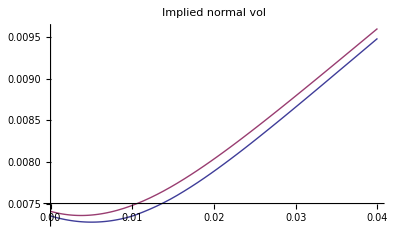
{45.692,-Graphics-}

```mathematica
Timing[Module[{S1=0.05,S2=0.03,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,ν1=0.01,ν2=0.01,M,Σinf,Σ,Q,βm,S,ρ,printflag=0,Lcoefs=LegendreCoeffs[40]},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
strikes={-0.02,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015,0.02}+0.02;
smile1=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,
BiHestonVanilla[S,strikes[[i]],τ,Σ,M,Σinf,β,ρ,printflag]]},{i,1,Length[strikes]}];
inter1=Interpolation[smile1,InterpolationOrder->2];
vol1=ImpVolHeston2[S1,S1,τ,Σ1,θ1,ρ1,-M1,ν1,Lcoefs];
vol2=ImpVolHeston2[S2,S2,τ,Σ2,θ2,ρ2,-M2,ν2,Lcoefs];ρsmod=ρs;
smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,LogNormalSpreadOption[S1,S2,vol1,vol2,ρsmod,strikes[[i]],τ]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
Plot[{inter1[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"biheston","bilog"},LegendPosition->{1,0}]
]]
```

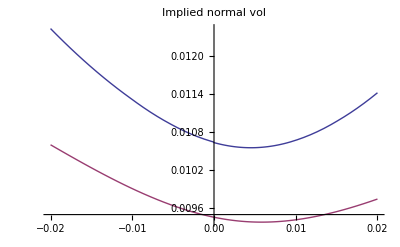
{45.927,-Graphics-}

```mathematica
Timing[Module[{S1=0.05,S2=0.05,M1=-0.01,M2=-0.02,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,ν1=0.01,ν2=0.01,M,Σinf,Σ,Q,βm,S,ρ,printflag=0,Lcoefs=LegendreCoeffs[40]},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
strikes={-0.02,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015,0.02};
smile1=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,
BiHestonVanilla[S,strikes[[i]],τ,Σ,M,Σinf,β,ρ,printflag]]},{i,1,Length[strikes]}];
inter1=Interpolation[smile1,InterpolationOrder->2];
vol1=ImpVolHeston2[S1,S1,τ,Σ1,θ1,ρ1,-M1,ν1,Lcoefs];
vol2=ImpVolHeston2[S2,S2,τ,Σ2,θ2,ρ2,-M2,ν2,Lcoefs];ρsmod=ρs;
smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,LogNormalSpreadOption[S1,S2,vol1,vol2,ρsmod,strikes[[i]],τ]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
Plot[{inter1[x],inter2[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"biheston","bilog"}]
]]
```

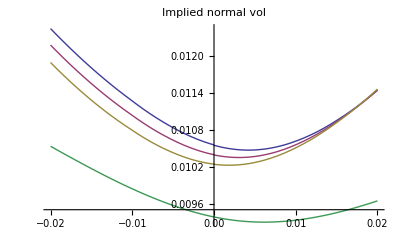
{137.078,-Graphics-}

```mathematica
Timing[Module[{S1=0.05,S2=0.05,M1=-0.05,M2=-0.05,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.3,ρm2=-0.3,ρ1=0.5,ρ2=0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,ν1=0.01,ν2=0.01,M,Σinf,Σ,Q,βm,S,ρ,printflag=0,Lcoefs=LegendreCoeffs[40],
smile1,smile2,smile3,inter1,inter2,inter3,smileLN,interLN},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
strikes={-0.02,-0.01,-0.005,-0.002,-0.001,-0.0005,-0.0002,-0.0001,0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015,0.02};
ρm1=-0.5;ρm2=-0.5;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile1=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,
BiHestonVanilla[S,strikes[[i]],τ,Σ,M,Σinf,β,ρ,printflag]]},{i,1,Length[strikes]}];
inter1=Interpolation[smile1,InterpolationOrder->2];
ρm1=-0.5;ρm2=0;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile2=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,
BiHestonVanilla[S,strikes[[i]],τ,Σ,M,Σinf,β,ρ,printflag]]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2,InterpolationOrder->2];
ρm1=-0.5;ρm2=0.5;
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});
smile3=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,
BiHestonVanilla[S,strikes[[i]],τ,Σ,M,Σinf,β,ρ,printflag]]},{i,1,Length[strikes]}];
inter3=Interpolation[smile3,InterpolationOrder->2];
vol1=ImpVolHeston2[S1,S1,τ,Σ1,θ1,ρ1,-M1,ν1,Lcoefs];
vol2=ImpVolHeston2[S2,S2,τ,Σ2,θ2,ρ2,-M2,ν2,Lcoefs];ρsmod=ρs;
smileLN=Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],τ,LogNormalSpreadOption[S1,S2,vol1,vol2,ρsmod,strikes[[i]],τ]]},{i,1,Length[strikes]}];
interLN=Interpolation[smileLN];
Plot[{inter1[x],inter2[x],inter3[x],interLN[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied normal vol",
PlotLegend->{"biheston --","biheston -0","biheston -+","bilog"},LegendPosition->{1,0}]
]]
```

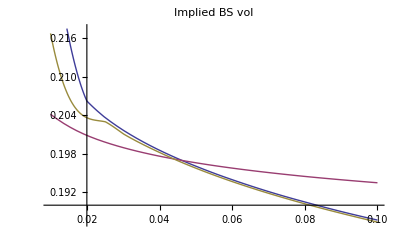
{237.309,-Graphics-}

```mathematica
Off[InterpolatingFunction::"dmval"];
Timing[Module[{S1=0.05,S2=0.04,M1=-0.05,M2=-0.06,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.,ρm2=0.,ρ1=-0.5,ρ2=-0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,M,Σinf,Σ,Q,βm,S,ρ,printflag=0,Lcoefs=LegendreCoeffs[40],
smile1,smile2,smile3,inter1,inter2,inter3,smileLN,interLN},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
strikes={0.01,0.02,0.025,0.03,0.035,0.04,0.045,0.048,0.05,0.055,0.06,0.08,0.1};
smile1=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,BiHestonUnderlying1Vanilla[S,strikes[[i]],τ,Σ,M,Σinf,β,ρ,printflag]]},{i,1,Length[strikes]}];
inter1=Interpolation[smile1,InterpolationOrder->2];
 Q=√(-M1 θ1)/β;
smile2=Table[{strikes[[i]],ImpVolHeston2[S1,strikes[[i]],τ,Σ1,θ1,ρ1,-M1,Q,Lcoefs]},{i,1,Length[strikes]}];
inter2=Interpolation[smile2];
smile3=Table[{strikes[[i]]+0.0001,ImpVolBS[S1,strikes[[i]]+0.0001,τ,BiHestonVanilla[{S1,0.0001},strikes[[i]],τ,Σ,M,Σinf,β,ρ,printflag]]},{i,1,Length[strikes]}];

inter3=Interpolation[smile3];
Plot[{inter1[x],inter2[x],inter3[x]},{x,strikes[[1]],Last[strikes]},PlotLabel->"Implied BS vol",
PlotLegend->{"BiHestonUnderlying1","Heston","Bihestonlimit"},LegendPosition->{1,0}]
]]
```

```mathematica
Off[InterpolatingFunction::"dmval"];
Timing[Module[{S1=0.05,S2=0.04,M1=-0.05,M2=-0.06,θ1=0.03,θ2=0.041,ρs=0.6,ρsinf=0.8,ρm1=0.,ρm2=0.,ρ1=-0.5,ρ2=-0.8, Σ1=0.04,Σ2=0.05,β=5,τ=5,λ1=1.1,λ2=1.2,M,Σinf,Σ,Q,βm,S,ρ,printflag={1,2,4,6},Lcoefs=LegendreCoeffs[40],
smile1,smile2,smile3,inter1,inter2,inter3,smileLN,interLN},
M=({{M1, ρm1 √(M1 M2)}, {ρm2 √(M1 M2), M2}});Σinf=({{θ1, √(θ1 θ2) ρsinf}, {√(θ1 θ2) ρsinf, θ2}});Σ=({{Σ1, √(Σ1 Σ2) ρs}, {√(Σ1 Σ2) ρs, Σ2}});S={S1,S2};ρ={ρ1,ρ2};
strikes={0.04};
smile1=Table[{strikes[[i]],ImpVolBS[S1,strikes[[i]],τ,BiHestonUnderlying1Vanilla[S,strikes[[i]],τ,Σ,M,Σinf,β,ρ,printflag]]},{i,1,Length[strikes]}];
smile3=Table[{strikes[[i]]+0.0001,ImpVolBS[S1,strikes[[i]]+0.0001,τ,BiHestonVanilla[{S1,0.0001},strikes[[i]],τ,Σ,M,Σinf,β,ρ,printflag]]},{i,1,Length[strikes]}];{smile1,smile3}
]]
```

{72.088,{{{0.04,0.198551661811462329983635615723}},{{0.0401,0.198182540003801270040680278273}}}}